# GABE (temp) NOTEBOOK : Means and Variances

Clear all variables to avoid naming conflicts.

```mathematica
ClearAll["Global`*"]
```

```mathematica
globalThickness=0.005;
globalFontSize=16;
globalFont="Latin Modern Mono Prop 10";
SetOptions[{ListPlot, ListLogPlot, Plot, LogPlot,ListLogLinearPlot,ListLogLogPlot,RegionPlot},LabelStyle->{ FontFamily->globalFont,FontSize-> globalFontSize, FontColor-> Black }, PlotStyle-> {Black, Thickness-> globalThickness}];
```

```mathematica
dirlabel="17445_64_1000_125"
plotlabel="17445";
```

17445_64_1000_125

## PARAMETERS: Set parameters for where to read data and what to plot

The number of labels should be at least as large as the number of fields. Additional labels will be ignored.

```mathematica
label[1]="ϕ";label[2]="h_1";label[3]="h_2";label[4]="h_3"; label[5]="h_4";
```

Whether to plot means and/or variances. 0=Don't plot, 1=Plot.

```mathematica
domeans=1;dovars=1;
```

The run variables are
  
dir - The directory where the files are stored

  ext - The extension of the data files
  nflds - The number of fields in the simulations
  skip - Number of points to skip between each plotted point. Used for making plots of large datasets

```mathematica
Clear[dir]
dir="C:\\Users\\admin\\Documents\\PhD_work\\R2HI\\Long paper\\GABE\\local_results_"<>dirlabel<>"\\slices\\";ext=".dat";nflds=5;
```

## RUN DATA: Read in data and make plots for each run

```mathematica
intablemv=ReadList[dir<>"meansvariances.dat", Table[Real, {13}]] ;(*last two: for radial component*)
numtimesmeans = Length[intablemv];

mmeanstable[1]=Table[{intablemv⟦i,1⟧,intablemv⟦i,2⟧},{i,1,numtimesmeans}];
mmeanstable[2] = Table[{intablemv⟦i,1⟧,intablemv⟦i,4⟧},{i,1,numtimesmeans}];
mmeanstable[3]=Table[{intablemv⟦i,1⟧,intablemv⟦i,6⟧},{i,1,numtimesmeans}];
mmeanstable[4]= Table[{intablemv⟦i,1⟧,intablemv⟦i,8⟧},{i,1,numtimesmeans}];
mmeanstable[5]= Table[{intablemv⟦i,1⟧,intablemv⟦i,10⟧},{i,1,numtimesmeans}];

tmax=mmeanstable[1][[numtimesmeans,1]]
```

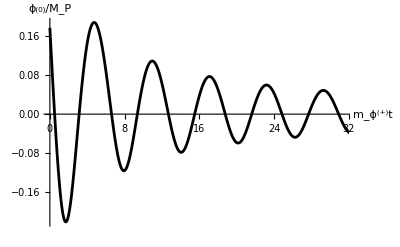

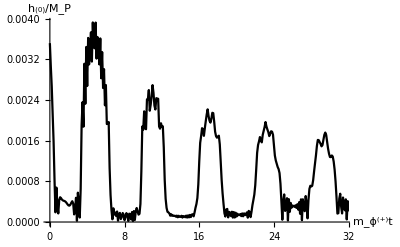

```mathematica
mmeansplot[1]=ListPlot[mmeanstable[1],Joined->True,AxesLabel->{"m_ϕ^(+)t","ϕ_(0)/M_P"}, PlotRange->{{0 ,10*Pi}, All}]
mmeansplot[2]=ListPlot[Table[{mmeanstable[2][[i,1]],Sqrt[(mmeanstable[2][[i,2]])^2+(mmeanstable[3][[i,2]])^2+(mmeanstable[4][[i,2]])^2+(mmeanstable[5][[i,2]])^2] },{i,1,Length[mmeanstable[2]]}],Joined->True,AxesLabel->{"m_ϕ^(+)t","h_(0)/M_P"},
			PlotStyle->{{Black,globalThickness}, {Black,Dashed,globalThickness}},
			 PlotRange->{{0,10*Pi},All}]
```

```mathematica
meanstable[1]=Table[{intablemv⟦i,1⟧,intablemv⟦i,2⟧^2},{i,1,numtimesmeans}];
meanstable[2] = Table[{intablemv⟦i,1⟧,intablemv⟦i,4⟧^2},{i,1,numtimesmeans}];
meanstable[3]=Table[{intablemv⟦i,1⟧,intablemv⟦i,6⟧^2},{i,1,numtimesmeans}];
meanstable[4]= Table[{intablemv⟦i,1⟧,intablemv⟦i,8⟧^2},{i,1,numtimesmeans}];
meanstable[5]= Table[{intablemv⟦i,1⟧,intablemv⟦i,8⟧^2},{i,1,numtimesmeans}];

varstable[1]=Table[{intablemv⟦i,1⟧,intablemv⟦i,3⟧},{i,1,numtimesmeans}];
varstable[2]=Table[{intablemv⟦i,1⟧,intablemv⟦i,5⟧},{i,1,numtimesmeans}];
varstable[3]=Table[{intablemv⟦i,1⟧,intablemv⟦i,7⟧},{i,1,numtimesmeans}];
varstable[4] = Table[{intablemv⟦i,1⟧,intablemv⟦i,9⟧},{i,1,numtimesmeans}];
varstable[5] = Table[{intablemv⟦i,1⟧,intablemv⟦i,9⟧},{i,1,numtimesmeans}];
```

```mathematica
tmax=meanstable[1][[Length[meanstable[1]], 1]];
```

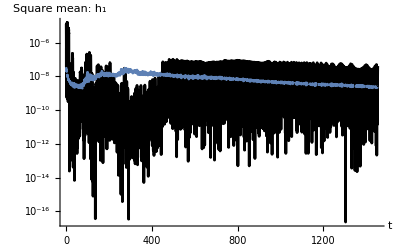

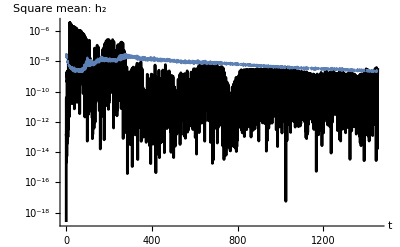

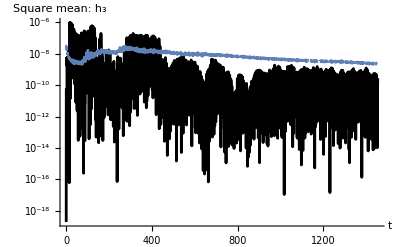

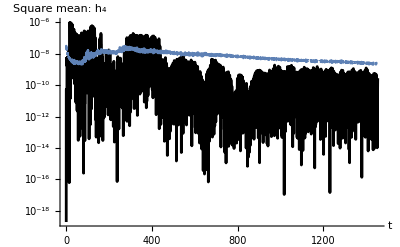

```mathematica
For[fld=2, fld<nflds+1, fld++,
Print[Show[{ListLogPlot[meanstable[fld], Joined->True], ListLogPlot[varstable[1],Joined-> True, PlotStyle->{Dashing[.01], Automatic}]}, PlotRange-> {{0,tmax}, All} ,AxesLabel->{"t","Square mean: "<>label[fld] }]]
]
```

Trajectory plot

```mathematica
l=.01;
b=1.7445*10^9;
xi1=Sqrt[(2*10^9 -b)*l];
V[x_,h_]:=3*(xi1^2+l*b)/l 1/4*Exp[-2*Sqrt[2/3]*x] *(  l*(h^2)^2 + 1/b( Exp[Sqrt[2/3]*x] -1 - xi1*(h^2  )  )^2  );
xFun=Interpolation[mmeanstable[1]];
hFun=Interpolation[mmeanstable[2]];
tDrop=t/.FindRoot[xFun'[t],{ t,1}]
tZero=t/.FindRoot[xFun[t], {t,3.5}]
tmax=4.5
tTachStart=3.15009;
tTachEnd=3.30812;
```

1.70524

3.13186

4.5

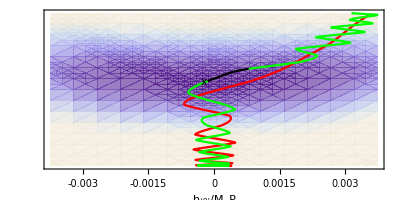

```mathematica
ticksy={-.2, -.1, 0, .1, .2};
ticksytabs=Table[{((-.2*1.1)/11)*i,""}, {i,-11, 11}];

ticksx={-0.003, -0.0015,0,0.0015, 0.003};
ticksxtabs=Table[{0.003*((i*1.2)/12), ""}, {i,-12, 12}];
hmax=hFun[t/.NMaximize[{hFun[t], t>0 && t<tmax}, t][[2]]];
xmin=xFun[t/.NMinimize[{xFun[t], t>0 && t<tmax}, t][[2]]];
xmax=xFun[t/.NMaximize[{xFun[t], t>0 && t<tmax}, t][[2]]];
trajectoryPlot=Show[{
DensityPlot[90V[ x,h], {h,-hmax,hmax}, {x,xmin,xmax},
	PlotStyle-> Opacity[.6],
	ColorFunctionScaling->False,
	ColorFunction->{"LakeColors"},
	FrameLabel-> {"h_(0)/M_P",None,None,"ϕ_(0)
/M_P"},
	LabelStyle->{FontFamily-> globalFont, globalFontSize, Black},
	RotateLabel->False,
	LabelStyle->{globalFontSize, FontFamily-> globalFont, Black},	
	PlotRangeClipping->False,
	AspectRatio->.5
	],
	ParametricPlot[{{hFun[t],xFun[t]}},{t,0,tDrop},
		 PlotRange->All,
		AspectRatio->.6, PlotStyle->Red,
		FrameTicks->None],
	ParametricPlot[{{hFun[t],xFun[t]}},{t,tDrop,tTachStart}, 
		PlotRange->{{-hmax,hmax}, {xmin,xmax}},
		AspectRatio->.6, PlotStyle->Green],
ParametricPlot[{{hFun[t],xFun[t]}},{t,tTachStart,tTachEnd}, 
		PlotRange->{{-hmax,hmax}, {xmin,xmax}},
		AspectRatio->.6, PlotStyle->Black,
		FrameTicks->None],
ParametricPlot[{{hFun[t],xFun[t]}},{t,tTachEnd,tmax}, 
		PlotRange->{{-hmax,hmax}, {xmin,xmax}},
		AspectRatio->.6, PlotStyle->Green,
		FrameTicks->None]
	},
Epilog-> {
		Style[Text["x",{hFun[tZero], xFun[tZero]}],FontFamily->"Arial", 24, Black] (*moment scalaron scrosses zero*)
		},
PlotRangeClipping-> False,
FrameTicks->{Union[ticksx, ticksxtabs], ticksytabs, ticksxtabs, Union[ticksy,ticksytabs]}
]
plotlabel="17445";
(*Export["trajectory_"<>plotlabel<>".pdf", trajectoryPlot]*)

"trajectory_17445.pdf"
```